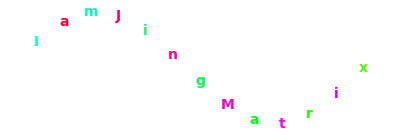

```mathematica
Show[Graphics[MapThread[Text[StyleForm[#1,FontFamily->"Courier",FontWeight->"Bold",
FontSize->14,FontColor->Hue@N[#2,4]],{#2,Sin@#2}]&,{Characters["IamJingMatrix"],Table[2(i Pi)/13,{i,1,13}]}]]]
```